## MICA: Measurement, Instrumentation, Control and Analysis

## Wiener System Identification: Sigmoid

#### Ian Hunter, MIT, 6 May 2026

#### Objectives

The purpose of this MICA Module is to define Wiener systems and introduce techniques which under certain circumstances enables Wiener systems to be characterized experimentally.

#### Wiener Systems

-Graphics-

A linear dynamic subsystem followed by a static nonlinearity (e.g., cuber, hard limiter, etc) is called a Wiener system after Norbert Wiener shown above (see https://en.wikipedia.org/wiki/Norbert_Wiener), the MIT mathematician who developed a number of system identification techniques. Wiener systems should not be confused with Wiener kernel nonlinear system representations.

-Graphics-

Here we see a Wiener system consisting of a linear dynamic subsystem as represented by an impulse response function, h(τ), follow by a static nonlinear element, n(·). The input to the Wiener system is denoted by, x(t), and the output from the Wiener system is denoted by, y(t). An internal signal u(t) is the output from the linear dynamic component, h(τ), and is also the input to the static nonlinear element, n(·).
Sometimes Wiener systems are called LN systems because there is a linear dynamic system (L) followed by a static nonlinearity (N). 

An NL system consists of a nonlinear static element (N) followed by a linear dynamic element (L) and is called a Hammerstein system. Hammerstein system identification is the subject of another MICA Notebook.

-Graphics-

In this MICA Notebook we will simulate a Wiener system and attempt to discover, h(τ) and n(·) purely from the input, x(t), and output, y(t), data sets.

#### Clear Symbols

We start by clearing any previously defined variables and symbols:

```mathematica
"■"; ClearAll["Global`*"]
```

#### Create Wiener system

As an example lets start by generating an impulse response function, h(τ), (to model the linear dynamic element) and lets make the nonlinear static element, n(·), a sigmoid function.

#### Generate h(τ)

Lets choose a second-order low-pass  subsystem. The general  transfer function  for such a  sub system is :

```mathematica
"■"; H[s_,α_,ω_,ζ_]:=(α ω^2)/(s^2+2 ζ ω s+ω^2)(* *)
```

If we inverse Laplace transform this transfer function then we get:

```mathematica
"■"; InverseLaplaceTransform[H[s,α,ω,ζ],s,τ]//FullSimplify
```

(ⅇ^(-ζ τ ω) α ω Sinh[√(-1+ζ^2) τ ω])/(√(-1+ζ^2))

This is the system continuous (or symbolic) unit impulse response function which we will denote h in order to distinguish it from the sampled version (see below) which we will denote, h. We also denote the continuous lag domain by τ to distinguish it from the sampled version  (see below) which is denoted by τi.

```mathematica
"■"; h[τ_,α_,ω_,ζ_]:=(ⅇ^(-ζ τ ω) α ω Sinh[√(-1+ζ^2) τ ω])/(√(-1+ζ^2))
```

Lets make the static gain, α = 1, the  natural frequency, ω = 60  rad/s  (around 10 Hz) , and the damping parameter  ζ = 0.7  .

```mathematica
"■"; h[τ_]:=h[τ,1,60,0.7]//FullSimplify//Re
```

Lets plot this:

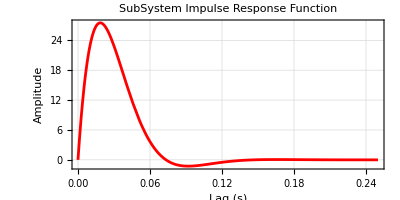

```mathematica
"■"; Plot[h[τ],{τ,0,0.25},PlotStyle->Red,Frame->True,GridLines->Automatic,LabelStyle->{12,Black},FrameLabel->{"Lag (s)","Amplitude"},AspectRatio->0.5,PlotLabel->"SubSystem Impulse Response Function",PlotRange->All,ImageSize->Automatic->600]
```

Notice that this impulse response function “dies out” by around 0.15 s.

We will need to sample this symbolic version of the impulse response function to produce a sampled version. To do this we need to specify the inter-sample interval, Δτ, and the maximum lag, τMax. Lets make the sampling increment be 2 ms (i.e., a sampling rate of 500 Hz) and the maximum lag be 0.25 s (as above).

```mathematica
"■"; Δτ=0.002; τMax=0.25;
```

We can now generate a sampled version of the lag domain, τ:

```mathematica
"■"; τi=Range[0,τMax, Δτ];
```

and a sampled version of the impulse response function:

```mathematica
"■"; hi=h[τi];
```

Now we can plot both the continuous and sampled versions of h:

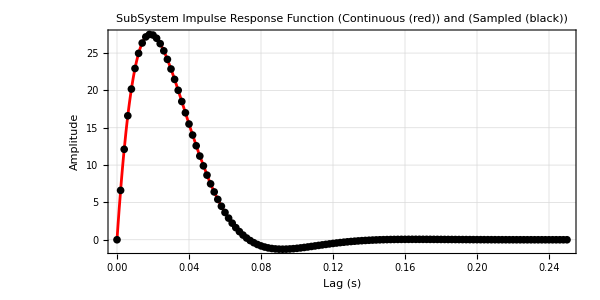

```mathematica
"■"; Show[
Plot[h[τ],{τ,0,0.25},PlotStyle->Red,Frame->True,LabelStyle->{12,Black},GridLines->Automatic,FrameLabel->{"Lag (s)","Amplitude"},AspectRatio->0.5,PlotLabel->"SubSystem Impulse Response Function (Continuous (red)) and (Sampled (black))",PlotRange->All,ImageSize->600],
ListPlot[{τi,hi}ᵀ,PlotStyle->Black]]
```

It is always a good idea to plot the individual points in the impulse response function to check that the sampling rate is high enough given the time course of the function. It is best to have plenty of points (e.g., > 5) covering the initial rise of the impulse response function. It is also best to have a domain (whose last value is τMax) which is 1.5 x to 2 x the time it takes for the impulse response to “die out”. If these conditions are not met then resample the original continuous (symbolic) impulse response function with a more appropriate sampling interval, Δτ, and maximum lag, τMax.

Note that the area under the impulse response function should equal the static gain, which is 1.0 in this case. Lets check by crude rectangular numeric integration:

```mathematica
"■";Total[hi] Δτ
```

0.998832

This is close enough.

#### Sigmoid static nonlinearity

In this example we will make the static nonlinearity a sigmoid with the following scaling and offset:

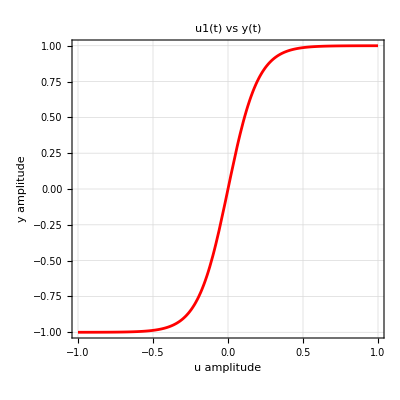

```mathematica
"■"; n[u_]:=2LogisticSigmoid[10 u]-1;
 Plot[n[u],{u,-1,1},GridLines->Automatic,PlotStyle->Red,Frame->True,LabelStyle->{12,Black},FrameLabel->{"u amplitude","y amplitude"},AspectRatio->1,PlotLabel->"u1(t) vs y(t)",PlotRange->All,ImageSize->400]
```

#### Generating the input, x(t), the unobservable internal signal, u(t) and the output, y(t)

#### Generate Gaussian white noise signal, x(t)

We start by generating 20 seconds of a Gaussian white noise input, x(t), sampled at around 500 Hz, with a mean of 0 and a standard deviation of 1. Note that we could have used pretty much any stochastic input here except a stochastic binary input (which is not sufficient to identify a nonlinear system). Note that as before we generate a sampled version of the time domain and specify a maximum time, tMax. Note also that we use the same sampling interval in time, Δt, as we used for lag, Δτ.

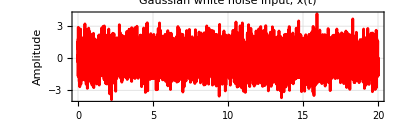

```mathematica
"■"; tMax=20.0;
Δt=Δτ;
ti=Range[0.0,tMax, Δt];
x=Table[RandomVariate[NormalDistribution[0,1]],Length[ti]]; 
ListLinePlot[{ti,x}ᵀ,PlotTheme->"Detailed",PlotRange->All, PlotStyle->Red,Frame->True,LabelStyle->{12,Black},FrameLabel->{"Time (s)","Amplitude"},AspectRatio->0.3,PlotLabel->"Gaussian white noise input, x(t)",ImageSize->Automatic->600]
```

#### Convolve, h(τ), with x(t) to produce, u(t)

We now numerically convolve our sampled input, x(t), with the sampled version of our impulse response function, h(τ), to generate the internal signal, u(t):

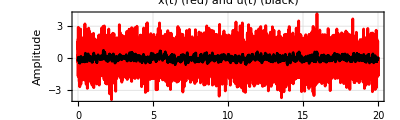

```mathematica
"■";u=Δt ListConvolve[hi,x,{1,1}] ;
ListLinePlot[{{ti,x}ᵀ,{ti,u}ᵀ},PlotTheme->"Detailed",PlotRange->All, PlotStyle->{Red, Black},Frame->True,LabelStyle->{12,Black},FrameLabel->{"Time (s)","Amplitude"},AspectRatio->0.3,PlotLabel->"x(t) (red) and u(t) (black)",ImageSize->Automatic->600]
```

#### Generate output, y(t)

We now pass u(t) through our static nonlinearity, n(), to produce the output, y(t):

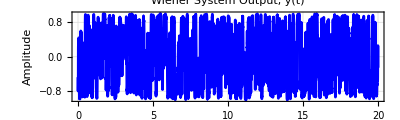

```mathematica
"■";y=n[u];
ListLinePlot[{ti,y}ᵀ,PlotTheme->"Detailed",PlotRange->All, PlotStyle->Blue,Frame->True,LabelStyle->{12,Black},FrameLabel->{"Time (s)","Amplitude"},AspectRatio->0.3,PlotLabel->"Wiener System Output, y(t)",ImageSize->Automatic->600]
```

#### Compare input and output probability density functions

We now calculate the input and output probability density functions using Mathematica’s SmoothHistogram[ ] function which determines the probability density functions via a different technique than the usual Histogram[ ] function. There is a whole area of statistics devoted to different probability density function determination methods.
Notice that while the original input, x(t) is Gaussian:

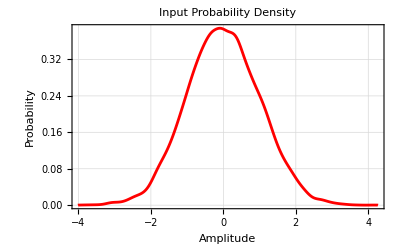

```mathematica
"■"; SmoothHistogram[x,Automatic,"PDF",PlotRange->All,PlotTheme->"Detailed",FrameLabel->{"Amplitude","Probability"},LabelStyle->{12,Black},PlotStyle->Red,PlotLabel->"Input Probability Density",ImageSize->Automatic->400]
```

The output, y(t), is clearly nonGaussian:

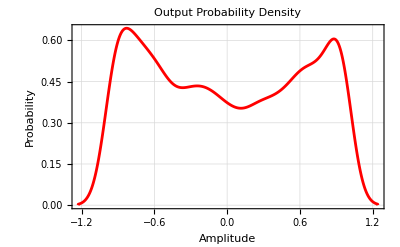

```mathematica
"■"; SmoothHistogram[y,Automatic,"PDF",PlotRange->All,PlotTheme->"Detailed",FrameLabel->{"Amplitude","Probability"},LabelStyle->{12,Black},PlotStyle->Red,PlotLabel->"Output Probability Density",ImageSize->Automatic->400]
```

A linear system perturbed by a Gaussian stochastic input (does not need to be white) will produce a Gaussian stochastic output. If the output from a system driven by a Gaussian stochastic input is non Gaussian (as here) then this is clear evidence that the system is nonlinear.

#### Compare input and output probability distribution functions

Lets calculate the smoothed input and output probability distribution functions:

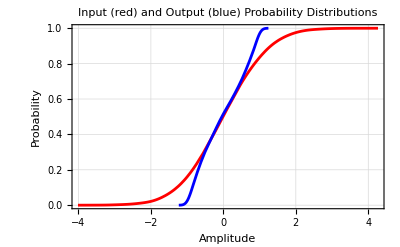

```mathematica
"■"; Show[
SmoothHistogram[x,Automatic,"CDF",PlotStyle->Red,PlotRange->All,PlotTheme->"Detailed",FrameLabel->{"Amplitude","Probability"},LabelStyle->{12,Black},PlotLabel->"Input (red) and Output (blue) Probability Distributions",ImageSize->Automatic->400],
SmoothHistogram[y,Automatic,"CDF",PlotStyle->Blue]]
```

#### Wiener system identification

We now ask if it is possible to determine the two internal subsystems, namely, h(τ) and n(·) solely from the input, x(t), and output, y(t), signals.
Lets see what happens when we compute the nonparametric impulse response function, hi1(τ), between the input, x(t), and the output, y(t).

To do this we compute the input auto-correlation function, xacf(τ), and the cross-correlation function between x(t) and y(t), xyccf(τ).

Define a function to perform biased auto- and cross-correlation functions (strictly speaking it calculates auto- and cross-covariance functions)

```mathematica
"■"; cor[x_,y_,m_]:= With[{n=Length[x],xMn=Mean[x],yMn=Mean[y]},Table[((x[[1;;n-j]]-xMn).(y[[1+j;;n]]-yMn)) /n,{j,0,m}] ]
```

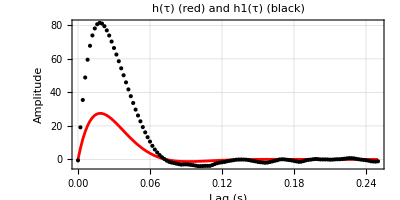

```mathematica
"■"; xacf=cor[x,x,τMax/Δt];
xyccf=cor[x,y,τMax/Δt];
toe=ToeplitzMatrix[xacf];
invtoe=Inverse[toe];
hi1=(invtoe.xyccf)/Δt;
ListPlot[{{τi,hi}ᵀ,{τi,hi1}ᵀ},Joined->{True,False},PlotTheme->"Detailed",PlotStyle->{Red,Black},Frame->True,LabelStyle->{12,Black},FrameLabel->{"Lag (s)","Amplitude"},AspectRatio->0.5,PlotLabel->"h(τ) (red) and h1(τ) (black)",PlotRange->All,ImageSize->Automatic->600]
```

If we multiply h(τ) by α and divide n(·) by α there will be no change in the output, y(t). In other words there is a scaling constant, α , that can freely move from h(τ) to n(·). So lets scale h1(τ) so that the area under it (i.e. the static gain) is 1:

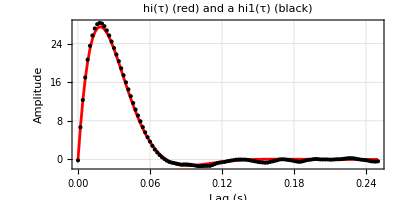

```mathematica
"■"; hi1=hi1/(Δτ Total[hi1]); (* scales hi1 to have unity static gain *)
ListPlot[{{τi,hi}ᵀ,{τi,hi1}ᵀ},Joined->{True,False},PlotTheme->"Detailed",PlotStyle->{Red,Black},Frame->True,LabelStyle->{12,Black},FrameLabel->{"Lag (s)","Amplitude"},AspectRatio->0.5,PlotLabel->"hi(τ) (red) and a hi1(τ) (black)",PlotRange->All,ImageSize->Automatic->600]
```

This is a remarkable result!! It shows that despite the presence of a major static nonlinearity such as a cuber, the stochastic system identification techniques were able to nevertheless get an estimate of the Wiener system’s dynamic linear element. This amazing result (for the case of cross-correlation) seems to have been first discovered by Julian Bussgang (https://en.wikipedia.org/wiki/Julian_J._Bussgang) in 1951 during his Master’s thesis research when he was a student at the Research Lab for Electronics (RLE) at MIT (https://en.wikipedia.org/wiki/Bussgang_theorem).

#### Predict u(t)

Now that we have h1(τ), we can convolve it with the input, x(t), to produce a prediction, u1(t), of the internal signal, u(t):

```mathematica
"■";u1=Δt ListConvolve[hi1,x,{1,1}] ;
```

#### Predict n(·)

Now that we have an estimate for u1(t) we can predict the form of the static nonlinearity by simply cross-plotting u1 vs y:

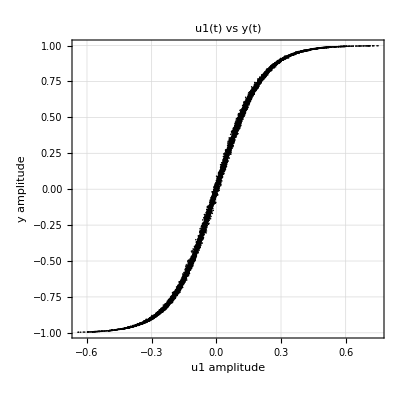

```mathematica
"■"; ListPlot[{u1,y}ᵀ,PlotTheme->"Detailed",PlotStyle->{Red,Black},Frame->True,LabelStyle->{12,Black},FrameLabel->{"u1 amplitude","y amplitude"},AspectRatio->1,PlotLabel->"u1(t) vs y(t)",PlotRange->All,ImageSize->400]
```

We can find an approximation to the estimate, n1(·), of n(·) above by fitting a high order polynomial to the u1(t) vs y(t) cross-plot:

```mathematica
"■"; n1=LinearModelFit[{u1,y}ᵀ, {1,uu,uu^3,uu^5,uu^7,uu^9},uu]["Function"];
```

Notice that we only used odd powers in this polynomial fit. The reasoning behind this will be explained in subsequent MICA notebooks.

Lets plot this estimate, n1(·), of the nonlinearity together with the cross-plot of u1(t) vs y(t):

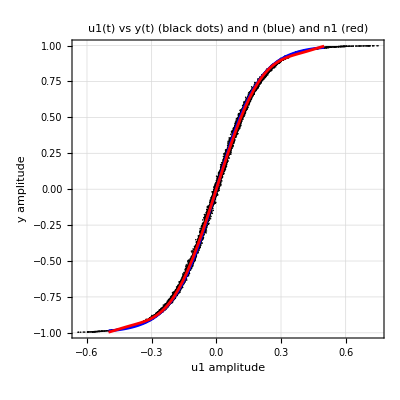

```mathematica
"■"; Show[
ListPlot[{u1,y}ᵀ,PlotTheme->"Detailed",PlotStyle->Black,Frame->True,LabelStyle->{12,Black},FrameLabel->{"u1 amplitude","y amplitude"},AspectRatio->1,PlotLabel->"u1(t) vs y(t) (black dots) and n (blue) and n1 (red)",PlotRange->All,ImageSize->400],
Plot[{n[uu],n1[uu]},{uu,-0.5,0.5},PlotStyle->{Blue,Red}]]
```

So as we can see our estimate of the Wiener system static nonlinearity, n1(·),  is close to the actual static nonlinear element, n(·).

Now that we have the estimate, n1(·), we can predict the output, y1(t), from our u1(t) estimate:

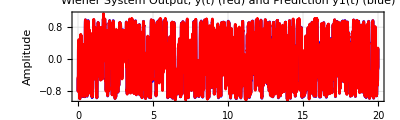

```mathematica
"■"; y1=n1[u1];
 ListLinePlot[{{ti,y}ᵀ,{ti,y1}ᵀ},PlotTheme->"Detailed",PlotRange->All, PlotStyle->{Blue,Red},Frame->True,LabelStyle->{12,Black},FrameLabel->{"Time (s)","Amplitude"},AspectRatio->0.3,PlotLabel->"Wiener System Output, y(t) (red) and Prediction y1(t) (blue)",ImageSize->Automatic->600]
```

The prediction is so good it is difficult to see the difference between y(t) and y1(t). So lets calculate the residuals, r1(t):

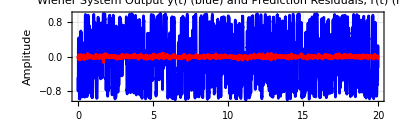

```mathematica
"■"; r1=y-y1;
ListLinePlot[{{ti,y}ᵀ,{ti,r1}ᵀ},PlotTheme->"Detailed",PlotRange->All, PlotStyle->{Blue,Red},Frame->True,LabelStyle->{12,Black},FrameLabel->{"Time (s)","Amplitude"},AspectRatio->0.3,PlotLabel->"Wiener System Output y(t) (blue) and Prediction Residuals, r(t) (red)",ImageSize->Automatic->600]
```

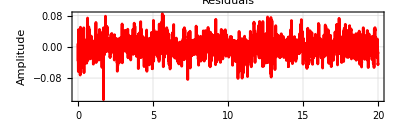

```mathematica
"■"; ListLinePlot[{ti,r1}ᵀ,PlotTheme->"Detailed",PlotRange->All, PlotStyle->Red,Frame->True,LabelStyle->{12,Black},FrameLabel->{"Time (s)","Amplitude"},AspectRatio->0.3,PlotLabel->"Residuals",ImageSize->Automatic->600]
```

```mathematica
"■"; vaf1=100.0 (1-Variance[r1]/Variance[y])
```

99.9057

At this point we could stop because the VAF is so high. However in this simulation of a Wiener system we did not add noise to our output (which would have decreased the VAF). We will therefor attempt to refine our estimates of h(τ) and n(·) to see if we can achieve an even higher VAF.

#### Function reversion (sometimes called function inversion)

There are many occasions in which given a function y = f(x) we want to find a function x = g(y). Function g() is often (including Mathematica) called the inverse function of f() and sometimes in mathematics texts it is called the reversion of f(). For example, you might have a function  voltage = f(temperature) relating the voltage generated by a thermocouple junction to its temperature. However if you measure the voltage across a thermocouple junction and wish to deduce the its temperature you need the inverse function, g(), so that given a voltage you can calculate the temperature via    temperature = g(voltage).

Many of the worlds most famous mathematicians have worked on the reversion problem including Gauss and Lagrange.
Mathematica has some powerful function reversion capabilities (under the functions InverseFunction[ ] and InverseSeries[ ].

For example, the reversion (or inverse) of  y = sin (x) is x = arcsin (y)

```mathematica
"■"; InverseFunction[Sin]
```

ArcSin

We would like to find the reversion of n1(·) so that given y(t) we can generate a new estimate, u2(t), of u(t).

A simple way to “invert” n1(·) is to refit the u1(t) vs y(t) but this time by reversing their roles to y(t) vs u1(t)as follows. Note that we use a “polynomial” with nth roots where n is odd. The reason for this will be explained in a subsequent MICA Notebook.

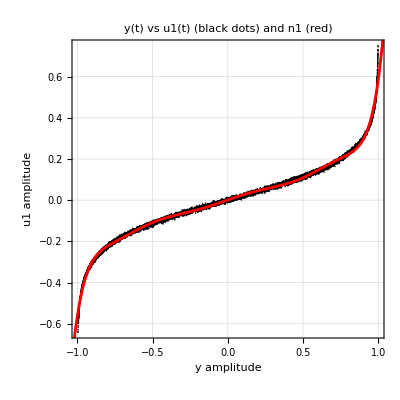

```mathematica
"■"; n1Inv=LinearModelFit[{y,u1}ᵀ, {1,uu,uu^2,uu^3,uu^4,uu^5,uu^6,uu^7,uu^8,uu^9},uu]["Function"];
Show[
ListPlot[{y,u1}ᵀ,PlotTheme->"Detailed",PlotStyle->Black,Frame->True,LabelStyle->{12,Black},FrameLabel->{"y amplitude","u1 amplitude"},AspectRatio->1,PlotLabel->"y(t) vs u1(t) (black dots) and n1 (red)",PlotRange->All,ImageSize->400],
Plot[n1Inv[uu],{uu,-5,5},PlotStyle->Red]]
```

Now that we have n1Inv we can generate a u2(t) from y(t):

```mathematica
"■";u2=n1Inv[y];
```

#### Re-estimate h(τ)

Now that we have u2(t) we can re-estimate h(τ):

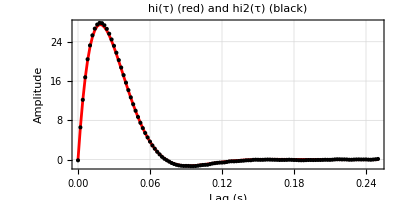

```mathematica
"■";xyccf=cor[x,u2,τMax/Δt];
hi2=(invtoe.xyccf)/Δt;
hi2=hi2/(Δτ Total[hi2]); (* scales hi2 to have unity static gain *)
ListPlot[{{τi,hi}ᵀ,{τi,hi2}ᵀ},Joined->{True,False},PlotTheme->"Detailed",PlotStyle->{Red,Black},Frame->True,LabelStyle->{12,Black},FrameLabel->{"Lag (s)","Amplitude"},AspectRatio->0.5,PlotLabel->"hi(τ) (red) and hi2(τ) (black)",PlotRange->All,ImageSize->Automatic->600]
```

Wow! Bang on.

#### Re-estimate u(t)

Now that we have the new impulse response function estimate, h2(t), we can convolve it with the input, x(t), to give a new estimate u3(t):

```mathematica
"■";u3=Δt ListConvolve[hi2,x,{1,1}] ;
```

#### Re-estimate n(·)

Now that we have a new estimate u3(t) we can predict the form of the static nonlinearity by simply cross-plotting u3 vs y:

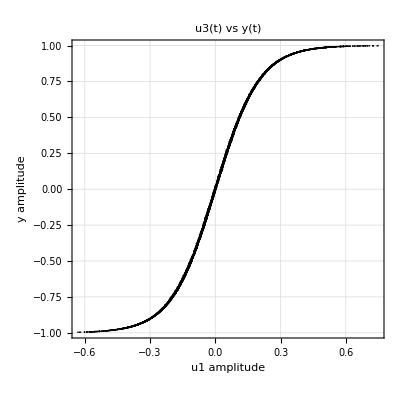

```mathematica
"■"; ListPlot[{u3,y}ᵀ,PlotTheme->"Detailed",PlotStyle->{Red,Black},Frame->True,LabelStyle->{12,Black},FrameLabel->{"u1 amplitude","y amplitude"},AspectRatio->1,PlotLabel->"u3(t) vs y(t)",PlotRange->All,ImageSize->400]
```

Notice that there is now much less scatter. This suggests that we are getting closer to want might be the true shape of the static nonlinearity.
We can find an approximation to the new estimate, n2(·) by fitting a high order polynomial (again with only odd powers) to the u3(t) vs y(t) cross-plot:

```mathematica
"■"; n2=LinearModelFit[{u3,y}ᵀ, {1,uu,uu^2,uu^3,uu^4,uu^5,uu^6,uu^7,uu^8,uu^9},uu]["Function"];
```

Lets plot this estimate, n2(·), of the nonlinearity together with the cross-plot of u3(t) vs y(t):

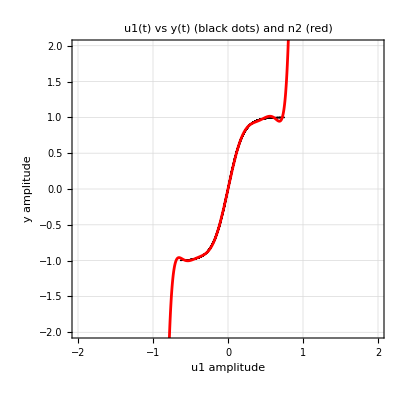

```mathematica
"■"; Show[
ListPlot[{u3,y}ᵀ,PlotTheme->"Detailed",PlotRange->{{-2,2},{-2,2}},PlotStyle->Black,Frame->True,LabelStyle->{12,Black},FrameLabel->{"u1 amplitude","y amplitude"},AspectRatio->1,PlotLabel->"u1(t) vs y(t) (black dots) and n2 (red)",PlotRange->All,ImageSize->400],
Plot[n2[uu],{uu,-1,1},PlotStyle->Red]]
```

So as we can see our estimate of the Wiener system static nonlinearity, n2(·),  is very close to the actual static nonlinear element, n(·), over the middle region of its range but on either side of this the fit is not good. This is typical of polynomial fits where the fit is good where there are plenty of data points (in the middle here) but degrades at the extremes.

Now that we have the new estimate, n2(·), we can predict the output, y2(t), from our u3(t) estimate:

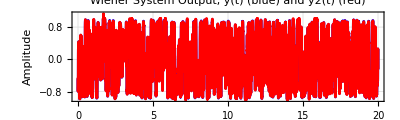

```mathematica
"■"; y2=n2[u3];
 ListLinePlot[{{ti,y}ᵀ,{ti,y2}ᵀ},PlotTheme->"Detailed",PlotRange->All, PlotStyle->{Blue,Red},Frame->True,LabelStyle->{12,Black},FrameLabel->{"Time (s)","Amplitude"},AspectRatio->0.3,PlotLabel->"Wiener System Output, y(t) (blue) and y2(t) (red)",ImageSize->Automatic->600]
```

The prediction is so good it is difficult to see the difference between y(t) and y2(t). So lets calculate the residuals, r2(t):

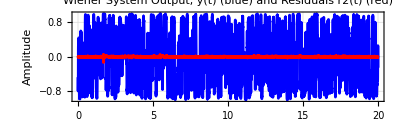

```mathematica
"■"; r2=y-y2;
ListLinePlot[{{ti,y}ᵀ,{ti,r2}ᵀ},PlotTheme->"Detailed",PlotRange->All, PlotStyle->{Blue,Red},Frame->True,LabelStyle->{12,Black},FrameLabel->{"Time (s)","Amplitude"},AspectRatio->0.3,PlotLabel->"Wiener System Output, y(t) (blue) and Residuals r2(t) (red)",ImageSize->Automatic->600]
```

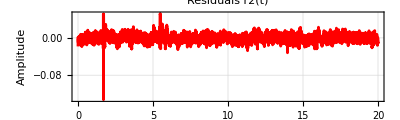

```mathematica
"■"; ListLinePlot[{ti,r2}ᵀ,PlotTheme->"Detailed",PlotRange->All, PlotStyle->Red,Frame->True,LabelStyle->{12,Black},FrameLabel->{"Time (s)","Amplitude"},AspectRatio->0.3,PlotLabel->"Residuals r2(t)",ImageSize->Automatic->600]
```

```mathematica
"■"; vaf2=100.0 (1-Variance[r2]/Variance[y])
```

99.9832

This VAF is so high there is no point in going any further other than to generate explicit parametric models for both the impulse response function and the static nonlinearity.

#### Parametric models

Now that we have a good nonparametric models for the impulse response function and the static nonlinearity it is appropriate to go one more step and generate parametric (equation based) models for both.

#### Parametric impulse response function model

By observation of the shape of hi2(τ) it looks as though it might be well approximated (fitted) by a second-order low-pass underdamped impulse response function.

```mathematica
"■"; h[τ_,α_,ω_,ζ_]:=(ⅇ^(-ζ τ ω) α ω Sinh[√(-1+ζ^2) τ ω])/(√(-1+ζ^2))
```

We start by defining an objective function to be minimized. Lets find the 3 parameters of the parametric second order low-pass underdamped impulse response function which minimize the sum of squared differences between it and the best nonparametric impulse response function model we determined, namely, h2(τ).

```mathematica
"■";rmsError[α_,ω_,ζ_]:=With[{n=Length[hi2]},Abs[Sqrt[((hi2-h[τi,α,ω,ζ]).(hi2-h[τi,α,ω,ζ]))/(n-2)]]]
```

From inspection of h2(τ) above lets estimate that the natural frequency will be near 7 Hz. Which in rad/s is  :

```mathematica
"■";ωω=2π 7.0;
```

The system is clearly only slightly underdamped (i.e., a little less than 1.0) so lets set it to be:

```mathematica
"■";ζζ=0.8;
```

The static gain (i.e., overall gain) is the area under the impulse response function which we forced to be 1, so lets set it to be:

```mathematica
"■";αα=1.0
```

1.

```mathematica
"■";rmsError[αα,ωω,ζζ] (* rms error before nonlinear least squares fit *)
```

3.60842

Now lets plot the parametric impulse response function with these estimates together with the nonparametric impulse response function, h2(τ):

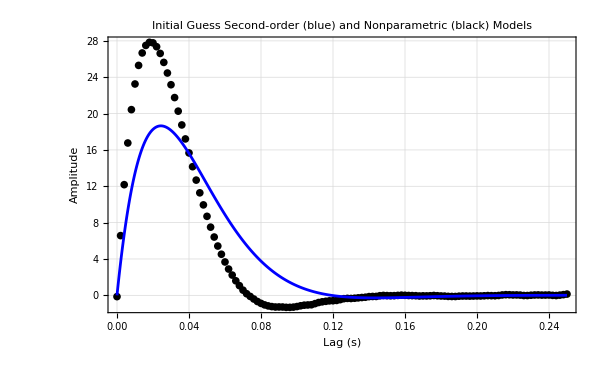

```mathematica
"■";Show[
ListPlot[{τi,hi2}ᵀ,PlotRange->All,Frame->True,PlotStyle->Black,LabelStyle->{12,Black},GridLines->Automatic,FrameLabel->{"Lag (s)","Amplitude"},PlotLabel->"Initial Guess Second-order (blue) and Nonparametric (black) Models", PerformanceGoal->"Quality",ImageSize->600],
Plot[h[τ,αα,ωω,ζζ],{τ,0,τMax},PlotStyle->Blue,PlotRange->All,PlotPoints->1000,PerformanceGoal->"Quality"]]
```

Our initial estimates are clearly off. Lets estimate the three parameters using our trusty Levenberg-Marquardt nonlinear minimization technique:

```mathematica
"■";nlm=NonlinearModelFit[{τi,hi2}ᵀ,h[τ,α,ω,ζ],{{α,αα},{ω,ωω},{ζ,ζζ}},τ, Method->"LevenbergMarquardt"];
nlm["BestFitParameters"]
{αα,ωω,ζζ}={α,ω,ζ}/.nlm["BestFitParameters"];
```

{α→1.01002,ω→60.008,ζ→0.696921}

```mathematica
"■";rmsError[αα,ωω,ζζ](* rms error after nonlinear least squares fit *)
```

0.0691726

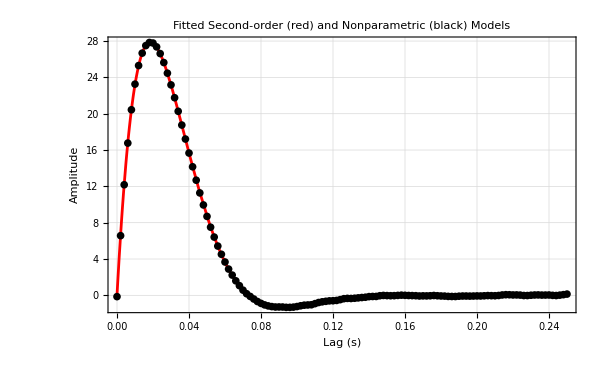

```mathematica
"■";Show[
Plot[h[τ,αα,ωω,ζζ],{τ,0,τMax},PlotRange->All,Frame->True,PlotStyle->Red,LabelStyle->{12,Black},GridLines->Automatic,FrameLabel->{"Lag (s)","Amplitude"},PlotLabel->"Fitted Second-order (red) and Nonparametric (black) Models", PerformanceGoal->"Quality",ImageSize->600],
ListPlot[{τi,hi2}ᵀ,PlotStyle->Black,PlotRange->All,PerformanceGoal->"Quality"]]
```

Nice! Clearly we have an excellent fit and there is no point going to a higher order model.

The original “true” values for the static gain, natural frequency and damping were:

```mathematica
{1,60,0.7}
```

The estimated values are

```mathematica
"■";{αα,ωω,ζζ}
```

{1.01002,60.008,0.696921}

These are almost exactly the same. So we have identified the parametric dynamic linear component of the Wiener system.

#### Parametric static nonlinear element model

It remains for us to find a parametric model for the static nonlinearity. The last estimate of the static nonlinearity was n2. Mathematica provides a function called FindFormula[ ] which attempts to discover static models which fit a data set. It takes a while because it is trying a huge number of candidate models:

```mathematica
"■"; fit=FindFormula[{u3,y}ᵀ,uu,10,All]
```

This discovery function returns static models together with a “Score” and a measure of “Complexity”. A “good” model is one which has a high Score (a good fit) but a low level of complexity under the assumption that simplicity is important. Most of the functions returned by FindFormula[ ] are way too complex and unfortunately the FindFormula[ ] function does not by default test for the LogisticSigmoid[ ] function. So lets assume that by looking at n2 we decided to try a LogisticSigmoid function then we could use our trusty Levenberg-Marquardt nonlinear minimization technique to fit this function to our data:

```mathematica
"■";nlm=NonlinearModelFit[{u3,y}ᵀ,p1 LogisticSigmoid[ p2 uu]-p3,{{p1,1.0},{p2,1.0},{p3,1.0}},uu, Method->"LevenbergMarquardt"];
nlm["BestFitParameters"]
{pp1,pp2,pp3}={p1,p2,p3}/.nlm["BestFitParameters"];
```

{p1→1.99967,p2→9.88214,p3→0.99973}

Compare with the actual parameters of the LogisticSigmoid function used in the Wiener system simulation:
p1 = 2,   p2 = 10,  p3 = 1  .
so we have almost exactly recover the three parameters of the static nonlinearity. However in a sense without our hunch that the form of the static nonlinearity was of a sigmoidal shape we would not have identified the nonlinearity and may have ended up with an overly complex static model.

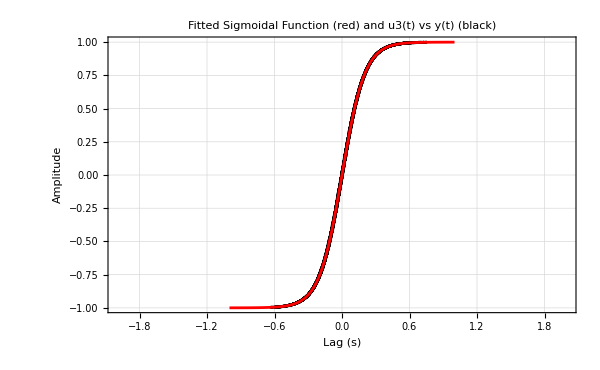

```mathematica
"■";Show[
ListPlot[{u3,y}ᵀ,PlotStyle->Black,PlotRange->{{-2,2},All},Frame->True,PlotStyle->Red,LabelStyle->{12,Black},GridLines->Automatic,FrameLabel->{"Lag (s)","Amplitude"},PlotLabel->"Fitted Sigmoidal Function (red) and u3(t) vs y(t) (black)", PerformanceGoal->"Quality",ImageSize->600,PerformanceGoal->"Quality"],
Plot[pp1 LogisticSigmoid[ pp2 uu]-pp3,{uu,-1,1},PlotRange->{{-2,2},All},PlotStyle->Red]]
```

#### Conclusion

In conclusion we have managed to identify both the linear dynamic part and the static nonlinear part of the the Wiener system. 
The Wiener system has been identified both non-parametrically and parametrically!!